## GetModel Example File

LGPL license applies. 
See http://xlr8r.info; http: for additional information.

```mathematica
<<xlr8r.m
```

```mathematica
<<CelleratorML.m
```

Read in the Cellerator Model from the file "rings.xml"; this file also refers to the Cellerator model in "ring.xml".

```mathematica
{model, parms, iv, opts}=GetModel["ring.xml"]
```

Model: Model4

CelleratorML Version: 1.0

3 reactions

2 parameters

3 initial values

{{{(X⟺XP)_ZP^Z,MM[K,v,K,v]},{(Y⟺YP)_XP^X,MM[K,v,K,v]},{(Z⟺ZP)_YP^Y,MM[K,v,K,v]}},{v→1,K→0.5},{X→1,Y→2,Z→3},{Name→Model4,Frozen→{}}}

```mathematica
sim=run[model, initialConditions-> iv, rates-> parms]
```

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {XP,YP,ZP}

{{X→InterpolatingFunction[{{0.,100.}},<>],XP→InterpolatingFunction[{{0.,100.}},<>],Y→InterpolatingFunction[{{0.,100.}},<>],YP→InterpolatingFunction[{{0.,100.}},<>],Z→InterpolatingFunction[{{0.,100.}},<>],ZP→InterpolatingFunction[{{0.,100.}},<>]}}

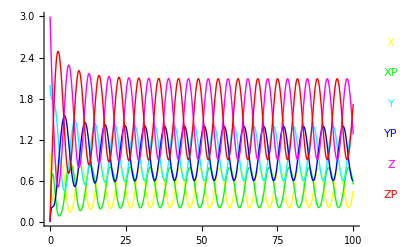

```mathematica
runPlot[sim]
```